```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\shiyi\work\git\fluc_T\fluctuations_T\highorder_2p1\parameters\v1_Tc260_alphap50\data

### Lattice

```mathematica
HotQCDp=Flatten[Import["../../../../LQCDdata/hotPT4.dat"]];
HotQCDT=Flatten[Import["../../../../LQCDdata/hotT.dat"]];
HotQCDperrdown=Flatten[Import["../../../../LQCDdata/hotdpt4d.dat"]];
HotQCDperrup=Flatten[Import["../../../../LQCDdata/hotdpt4u.dat"]];
Tcl=156;
Hotpdown=Transpose[{HotQCDT/Tcl,HotQCDp+HotQCDperrdown}];
Hotpup=Transpose[{HotQCDT/Tcl,HotQCDp+HotQCDperrup}];
WBp=Flatten[Import["../../../../LQCDdata/wbpt4.dat"]];
WBdp=Flatten[Import["../../../../LQCDdata/wbdpt4.dat"]];
WBT=Flatten[Import["../../../../LQCDdata/wbT.dat"]];
WBdown=Transpose[{WBT/Tcl,WBp-WBdp}];
WBup=Transpose[{WBT/Tcl,WBp+WBdp}];
WBcs=Table[Import["../../../../LQCDdata/WB-EoS.dat"][[i]][[-2]],{i,2,63}];
WBcserr=Table[Import["../../../../LQCDdata/WB-EoS.dat"][[i]][[-1]],{i,2,63}];
WBcsup=Transpose[{WBT/Tcl,WBcs+WBcserr}];
WBcsdown=Transpose[{WBT/Tcl,WBcs-WBcserr}];
WBp2025=Flatten[Import["../../../../LQCDdata/WB2025/PT4WB.dat"]];
WBdp2025=Flatten[Import["../../../../LQCDdata/WB2025/PT4WB_erro.dat"]];
WBT2025=Flatten[Import["../../../../LQCDdata/WB2025/TWB.dat"]];
WBdown2025=Transpose[{WBT2025/Tcl,WBp2025-WBdp2025}];
WBup2025=Transpose[{WBT2025/Tcl,WBp2025+WBdp2025}];
```

### Model

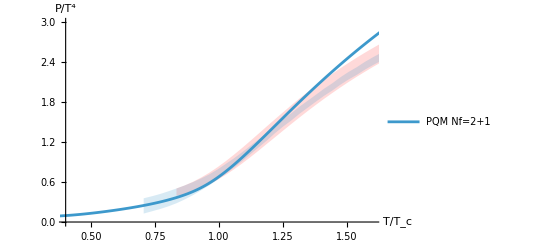

```mathematica
chi0=Flatten[Import["./chi0.dat"]];
chi1=Flatten[Import["./chi1.dat"]];
chi2=Flatten[Import["./chi2.dat"]];
chi3=Flatten[Import["./chi3.dat"]];
chi4=Flatten[Import["./chi4.dat"]];
chi5=Flatten[Import["./chi5.dat"]];
chi6=Flatten[Import["./chi6.dat"]];
chi7=Flatten[Import["./chi7.dat"]];
chi8=Flatten[Import["./chi8.dat"]];
T=Flatten[Table[21+(i-1),{i,1,280}]];
(*c0=Transpose[{T/184,chi0/T^4}];
c1=Transpose[{T,-4*chi0/T^5+chi1/T^4}];
c2=Transpose[{T,20*chi0/T^6-8*chi1/T^5+chi2/T^4}];
c3=Transpose[{T,-(120 chi0)/T^7+(60 chi1)/T^6-(12 chi2)/T^5+chi3/T^4}];
c4=Transpose[{T,(840 chi0)/T^8-(480 chi1)/T^7+(120 chi2)/T^6-(16 chi3)/T^5+chi4/T^4}];
cs2=Transpose[{T/184,chi1/(T*chi2)}];*)
PlotP=Show[ListLinePlot[{Transpose[{T/183,(chi0-chi0[[1]])/T^4}],Hotpdown,Hotpup},Filling->{2->{3}},FillingStyle->LightRed,PlotStyle->{Automatic,None,None},PlotLegends->{"PQM Nf=2+1"},PlotRange->{{0.4,1.6},{0,3}}],ListLinePlot[{WBdown,WBup},Filling->{1->{2}},PlotStyle->{None}],AxesLabel->{"T/T_c","P/T^4"}]
```

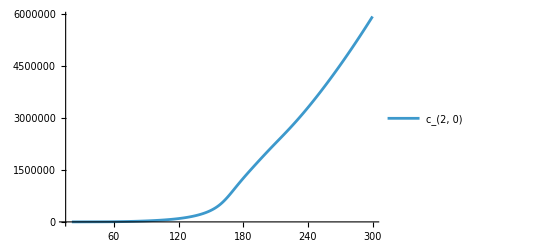

```mathematica
ListLinePlot[Transpose[{T,chi2}],PlotRange->All,PlotLegends->{"c_(2, 0)"}]
```

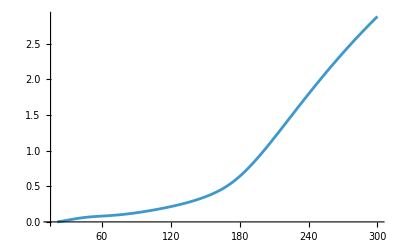

```mathematica
ListLinePlot[Transpose[{T,(chi0-chi0[[1]])/T^4}],PlotRange->All]
```

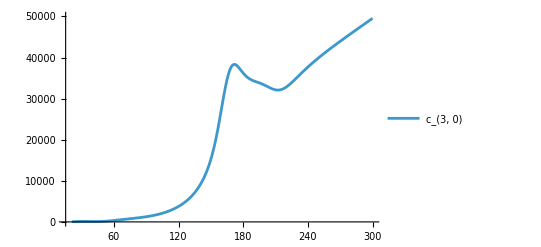

```mathematica
ListLinePlot[Transpose[{T,chi3}],PlotRange->{All,{-0000,50000}},PlotLegends->{"c_(3, 0)"}]
```

### Plot

ListLinePlot::lpn: {{},{«1»},{{0.833333,0.504},{0.865385,0.55},{0.897436,0.604},{0.929487,0.668},{0.961538,0.74},{0.99359,0.823},{1.02564,0.913},{1.05769,1.01},{1.08974,1.112},{1.12179,1.218},{1.15385,1.326},«29»,{2.11538,3.475},{2.14744,3.514},{2.17949,3.552},{2.21154,3.588},{2.24359,3.623},{2.27564,3.656},{2.30769,3.689},{2.33974,3.72},{2.37179,3.751},{2.40385,3.781},«5»}} 不是由数字或者数对组成的列表.

Show::gcomb: 无法合并 Show[«1»] 中的图形对象.

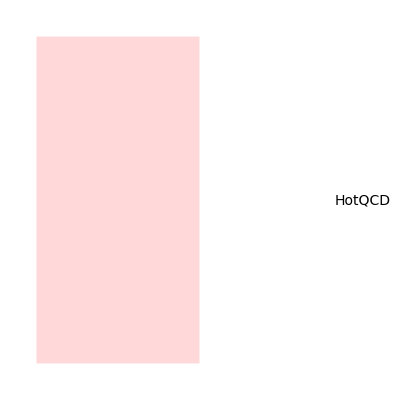
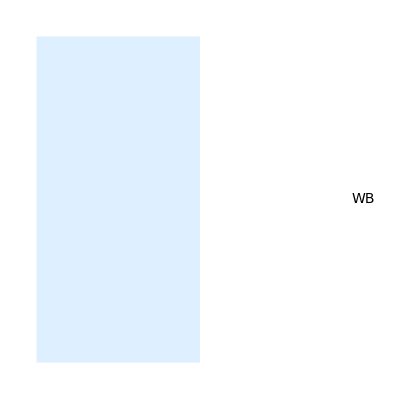
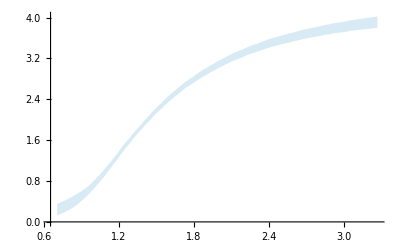
Show[ListLinePlot[{c0,{{0.833333,0.395},{0.865385,0.414},{0.897436,0.457},{0.929487,0.508},{0.961538,0.566},{0.99359,0.633},{1.02564,0.708},{1.05769,0.79},{1.08974,0.879},{1.12179,0.973},{1.15385,1.071},{1.1859,1.172},{1.21795,1.272},{1.25,1.373},{1.28205,1.473},{1.3141,1.571},{1.34615,1.667},{1.37821,1.76},{1.41026,1.851},{1.44231,1.938},{1.47436,2.023},{1.50641,2.105},{1.53846,2.184},{1.57051,2.259},{1.60256,2.333},{1.63462,2.403},{1.66667,2.47},{1.69872,2.536},{1.73077,2.599},{1.76282,2.66},{1.79487,2.718},{1.82692,2.774},{1.85897,2.829},{1.89103,2.881},{1.92308,2.932},{1.95513,2.981},{1.98718,3.028},{2.01923,3.073},{2.05128,3.117},{2.08333,3.16},{2.11538,3.2},{2.14744,3.239},{2.17949,3.278},{2.21154,3.315},{2.24359,3.351},{2.27564,3.385},{2.30769,3.418},{2.33974,3.451},{2.37179,3.482},{2.40385,3.513},{2.4359,3.541},{2.46795,3.569},{2.5,3.597},{2.53205,3.623},{2.5641,3.65}},{{0.833333,0.504},{0.865385,0.55},{0.897436,0.604},{0.929487,0.668},{0.961538,0.74},{0.99359,0.823},{1.02564,0.913},{1.05769,1.01},{1.08974,1.112},{1.12179,1.218},{1.15385,1.326},{1.1859,1.435},{1.21795,1.542},{1.25,1.649},{1.28205,1.754},{1.3141,1.856},{1.34615,1.953},{1.37821,2.048},{1.41026,2.139},{1.44231,2.227},{1.47436,2.312},{1.50641,2.392},{1.53846,2.471},{1.57051,2.546},{1.60256,2.618},{1.63462,2.688},{1.66667,2.755},{1.69872,2.819},{1.73077,2.882},{1.76282,2.942},{1.79487,2.999},{1.82692,3.055},{1.85897,3.109},{1.89103,3.161},{1.92308,3.211},{1.95513,3.259},{1.98718,3.306},{2.01923,3.35},{2.05128,3.394},{2.08333,3.436},{2.11538,3.475},{2.14744,3.514},{2.17949,3.552},{2.21154,3.588},{2.24359,3.623},{2.27564,3.656},{2.30769,3.689},{2.33974,3.72},{2.37179,3.751},{2.40385,3.781},{2.4359,3.808},{2.46795,3.836},{2.5,3.862},{2.53205,3.888},{2.5641,3.914}}},Filling→{2→{3}},FillingStyle→RGBColor[1, 0.85, 0.85],PlotStyle→{Automatic,None,None},PlotLegends→{PQM Nf=2+1},PlotRange→{{0.4,1.6},{0,3}}],-Graphics-,-Graphics-,-Graphics-,AxesLabel→{T/T_c,P/T^4}]

```mathematica
PlotP=Show[ListLinePlot[{c0,Hotpdown,Hotpup},Filling->{2->{3}},FillingStyle->LightRed,PlotStyle->{Automatic,None,None},PlotLegends->{"PQM Nf=2+1"},PlotRange->{{0.4,1.6},{0,3}}],Graphics[{Text[Style["HotQCD",14],{0.9,2.5}],LightRed,Rectangle[{0.5,2.3},{0.7,2.7}]}],Graphics[{Text[Style["WB",14],{0.9,1.8}],LightBlue,Rectangle[{0.5,1.6},{0.7,2.}]}],ListLinePlot[{WBdown,WBup},Filling->{1->{2}}(*,FillingStyle->LightBlue*),PlotStyle->{None,None}],AxesLabel->{"T/T_c","P/T^4"}]
```

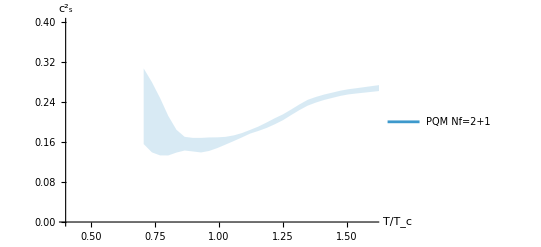

```mathematica
Plotcs2=Show[ListLinePlot[{cs2},FillingStyle->LightRed,PlotStyle->{Automatic,Automatic,None,None},PlotLegends->{"PQM Nf=2+1"},PlotRange->{{0.4,1.6},{0,0.4}}],ListLinePlot[{WBcsdown,WBcsup},Filling->{1->{2}},PlotStyle->{None}],AxesLabel->{"T/T_c","(c^2)_s"}]
```

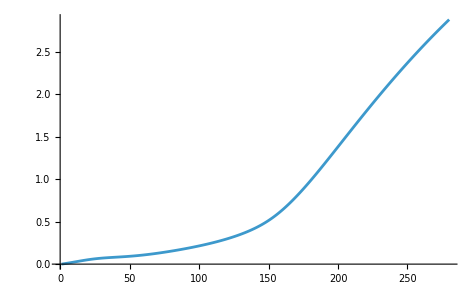

```mathematica
plotc0=ListLinePlot[chi0/T^4]
```

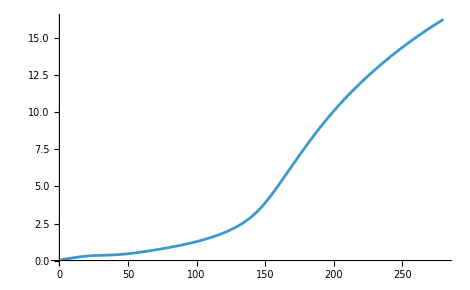

```mathematica
plotc1=ListLinePlot[chi1/T^3]
```

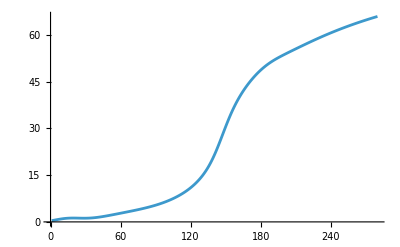

```mathematica
plotc2=ListLinePlot[chi2/T^2]
```

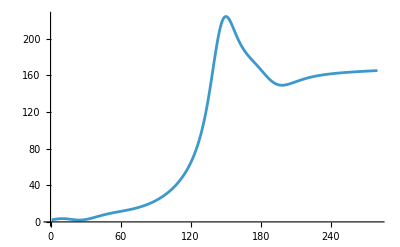

```mathematica
plotc3=ListLinePlot[chi3/T]
```

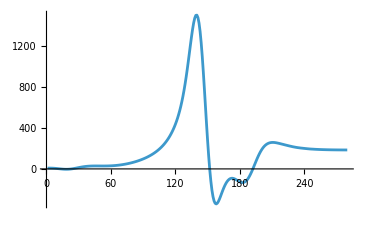

```mathematica
plotc4=ListLinePlot[chi4,PlotRange->All]
```

```mathematica
Export["./PoT4.pdf",PlotP];
Export["./cs2.pdf",Plotcs2];
Export["./c1.pdf",plotc1];
Export["./c2.pdf",plotc2];
Export["./c3.pdf",plotc3];
Export["./c4.pdf",plotc4];
```

## Temperature Fluctuations

```mathematica
c1=chi1;
c2=T^2(1/chi2)^1;
c3=-T^5(1/chi2)^3(chi3);
c4=T^8(3(1/chi2)^5(chi3)^2-(1/chi2)^4 chi4);
```

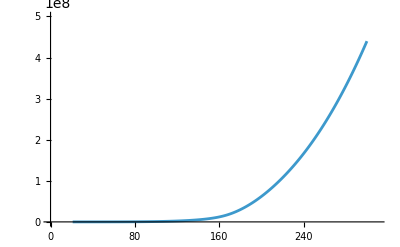

```mathematica
ListLinePlot[Transpose[{T,chi1}],PlotRange->{{0,310},{0.01,5*10^8}},ScalingFunctions->Automatic]
```

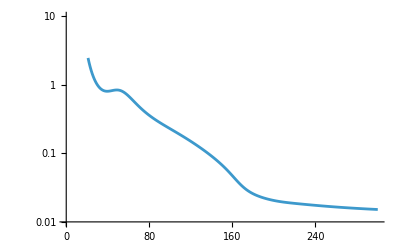

```mathematica
ListLinePlot[Transpose[{T,c2}],PlotRange->{{0,300},{0.01,10}},ScalingFunctions->"Log"]
```

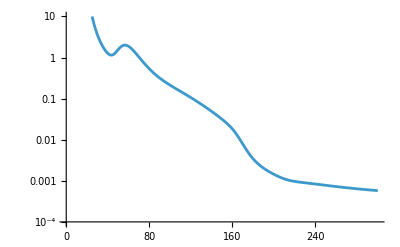

```mathematica
ListLinePlot[Transpose[{T,-c3}],PlotRange->{{0,300},{10,0.0001}},ScalingFunctions->"Log"]
```

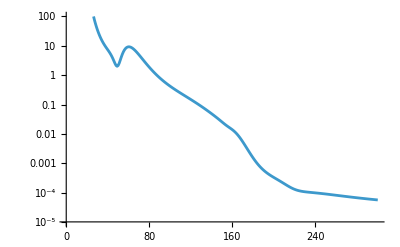

```mathematica
ListLinePlot[Transpose[{T,c4}],PlotRange->{{0,300},{0.00001,100}},ScalingFunctions->"Log"]
```